```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"fixtures","dataset.csv"}]];
```

```mathematica
extractDataByYear[l_List,y_Integer]:=Select[l,DateValue[First[#],"Year"]==DateValue[{y},"Year"]&]
```

```mathematica
extractDataByWeekday[l_List,w_Symbol]:=
Select[l,DayName[First[#]]==w&]
```

```mathematica
extractHourlyData[l_List]:=Map[Rest,l]
```

```mathematica
plotListWithModel[l_List,nlm_FittedModel]:=Show[Map[ListPlot,l],Plot[nlm[x],{x,0,24}],Range->All,Ticks->{Range[24],Automatic}]
```

```mathematica
getSampleData[l_List,y_Integer,w_Symbol,n_Integer]:=extractHourlyData[extractDataByWeekday[extractDataByYear[data,y],w]][[n]]
```

```mathematica
minMaxMeanPlot[l_List]:=Show[ListPlot[Map[Max,l],PlotStyle->Red],ListPlot[Map[Min,l],PlotStyle->Blue],ListPlot[Map[Mean,l],PlotStyle->Green],PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[getSampleData[data,2015,Monday,24],a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
```

FittedModel[1110.41-1073.15 x+255.375 «1»-16.7501 x^3+0.329474 x^4]

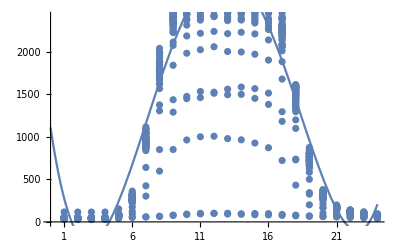

```mathematica
plotListWithModel[extractHourlyData[extractDataByWeekday[extractDataByYear[data,2015],Monday]],nlm]
```

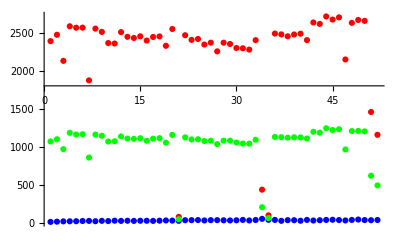

```mathematica
minMaxMeanPlot[extractHourlyData[extractDataByWeekday[extractDataByYear[data,2014],Monday]]]
```